I’m not presently using any machinery from “2023-12-04 Plot LPS for L1 L2 phase sweeps v2.nb” but that’ll give nicer results

## Single

```mathematica
raw = Import["~/tmpSLACData/BEGBC14_1_395.57678257581125.h5","Data"];
Keys[raw]
```

{/momentum/x,/momentum/y,/momentum/z,/position/x,/position/y,/position/z,/time,/weight}

```mathematica
rawToAssoc[raw_]:=(
data=Table[
Association[
{
"x"->raw[["/position/x",i]],
"y"->raw[["/position/y",i]],
"z"->raw[["/position/z",i]],

"px"->raw[["/momentum/x",i]],
"py"->raw[["/momentum/y",i]],
"pz"->raw[["/momentum/z",i]]
}
],
{i,Length[raw[["/momentum/x"]]]}
];
data)
```

```mathematica
data=rawToAssoc[raw];
```

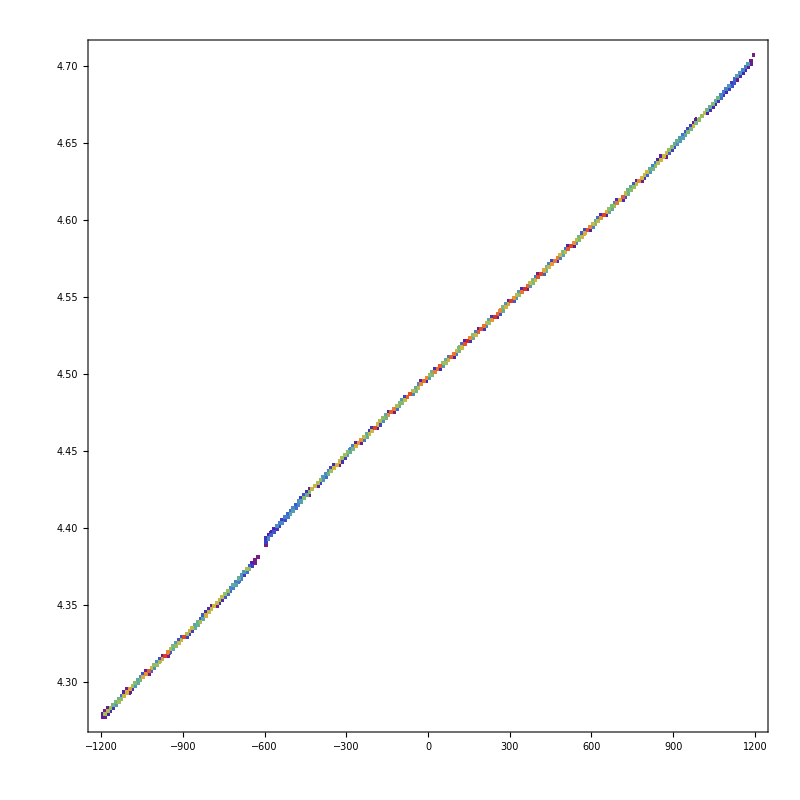

```mathematica
DensityHistogram[
{1*^6 * #z,1*^-9*#pz}&/@data,
{200,200},
ColorFunction->"Rainbow",
LabelStyle->20,
ImageSize->800
]
```

## Automate

```mathematica
fileNames = FileNames["~/tmpSLACData/*_*.h5"];
fileNameToKey[fileName_]:=(
{markerString,sPosition}=StringSplit[fileName,{"/",".h5","_"}][[-2;;-1]];
{markerString,ToExpression[sPosition]}
)
```

```mathematica
results = Association[
Table[
fileNameToKey[fileName]-> rawToAssoc[Import[fileName,"Data"]],
{fileName,fileNames}
]
];
```

```mathematica
orderedKeys = SortBy[Keys[results],Last]
```

{{OUTCPBF,7.89498},{BEGDL10,7.9559},{ENDINJ,7.9559},{FLNGBF2,7.9559},{L0BFEND,7.9559},{L0BFWAKE,7.9559},{IM10431,8.18188},{LH10BEG,8.63435},{HTRUNDF,9.44442},{LH10END,10.248},{WS10561,14.0212},{MRK0F,14.1289},{IM10591,14.7934},{BX0FBEG,16.7503},{BX0FEND,18.7179},{CNT0F,18.7179},{IM10791,19.7332},{BEGL1F,19.8907},{ENDDL10,19.8907},{L1XFEND,39.3796},{1,39.6432},{ENDL1F,39.6432},{BC11CBEG,40.4123},{1,46.948},{2,46.948},{BC11CEND,46.948},{CNT1B,46.948},{IM11360,47.6181},{2,53.9116},{BEGL2F,53.9116},{LI11STRT,53.9116},{WS11444,65.8882},{WS11614,81.131},{WS11744,102.921},{LI11END,118.478},{LI12BEG,118.478},{WS12214,133.353},{LI12END,220.078},{LI13BEG,220.078},{LI13END,321.678},{LI14BEG,321.678},{1,395.577},{ENDL2F,395.577},{1,398.268},{BEGBC14E,398.268},{2,421.299},{CNT2B,421.299},{ENDBC14E,421.299},{IM14890,422.458},{VV14940,423.017},{1,423.296},{2,423.296},{LI15BEG,423.296},{LI15END,524.896},{LI16BEG,524.896},{LI16END,626.496},{LI17BEG,626.496},{LI17END,728.096},{LI18BEG,728.096},{WS18944,827.81},{LI18END,829.696},{LI19BEG,829.696},{WS19144,841.798},{WS19244,854.142},{WS19344,866.487},{1,878.124},{2,878.124},{MSCAVEXT,878.124},{HLAM,904.682},{IM1988,929.229},{2,929.537},{BEGBC20,929.537},{LI19TERM,929.537},{CB1LE,930.6},{IM2040,934.466},{CB2LE,941.776},{MSEP1E,941.776},{AS1EL,943.288},{AS2EL,946.101},{CB3LE,953.682},{MCE,954.079},{CB3RE,955.005},{AS2ER,962.061},{AS1ER,964.861},{MSEP2E,966.382},{CB2RE,968.207},{IM2452,973.689},{BEGFF20,978.621},{CB1RE,978.621},{ENDBC20,978.621},{MFFF,979.005},{KRK,983.324},{DBMARK67,984.04},{BEGEXPT20,992.39},{ENDFF20,992.39},{EXTHOLE1,992.463},{IQMON20,992.823},{BEWIN1,992.883},{LCUBE,993.003},{CENT,993.723},{FILG,994.125},{FILS,994.177},{MIP,994.773},{PENT,994.773},{PEXT,995.943},{IM3255,996.893},{BEWIN2,997.003},{BEGSPECT20,997.183},{ENDEXPT20,997.183},{BEGPDC,1008.91},{ENDPDC,1010.27},{BEGEDC,1011.4},{ENDEDC,1011.9},{BFLYMID,1016.21},{EXTWIN,1016.44},{DBMARK30,1020.11},{ENDSPECT20,1020.11}}

```mathematica
standardizedPlotting[data_,title_]:=DensityHistogram[
{1*^6 * #z,1*^-9*#pz}&/@data,
{200,200},
ColorFunction->"Rainbow",
LabelStyle->20,
ImageSize->400,
(*PlotRange->{{-500,500},{9.7,10.2}},*)
PlotLabel->title
]
```

```mathematica
imgArr=Table[
standardizedPlotting[
results[key],
key
],
{key,orderedKeys}
];
```

```mathematica
Export["~/markersOnly.gif",imgArr]
```

~/markersOnly.gif